(ⅇ^(ⅈ x-x^2/24))/(2 (3 π)^(1/4))

(ⅇ^(-ⅈ x-x^2/24))/(2 (3 π)^(1/4))

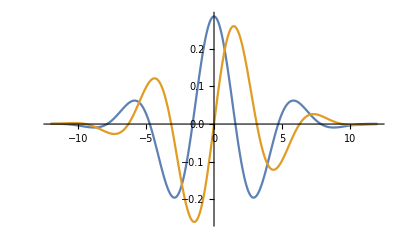

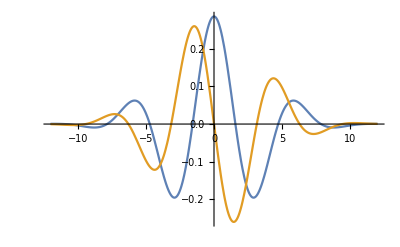

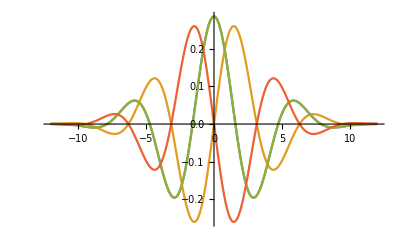

```mathematica
m=1;
γu=1;
γv=-1;
c=1;
yNorm[y_,z_]:=y/Sqrt[Integrate[Conjugate[y]y+Conjugate[z]z,{x,-Infinity,Infinity}]]
zNorm[y_,z_]:=z/Sqrt[Integrate[Conjugate[y]y+Conjugate[z]z,{x,-Infinity,Infinity}]]

y=yNorm[ⅇ^(-x^2/24+I m γu x),ⅇ^(-x^2/24+I m γv x)]
z=zNorm[ⅇ^(-x^2/24+I m γu x),ⅇ^(-x^2/24+I m γv x)]

Plot[{Re[y],Im[y]},{x,-12,12},PlotRange->All]
Plot[{Re[z],Im[z]},{x,-12,12},PlotRange->All]
Plot[{Re[y],Im[y],Re[z],Im[z]},{x,-12,12},PlotRange->All]
```